```mathematica
Ep = 1108;
```

```mathematica
measCond = 1.55*^-9;
```

```mathematica
preFactor = 2.680594*^-08;
```

```mathematica
qMaxF[Ep_,Tm_]:=1+2(√(Ep/Tm))/Erfc[-√(Ep/Tm)] NIntegrate[Erfc[x],{x,-√(Ep/Tm),∞}]
```

```mathematica
funker[Ep_,Tm_,κ_,Kmeas_]:=Kmeas/preFactor * √Tm *qMaxF[Ep,Tm]*((κ-3/2)^(1/2)Gamma[κ-1/2])/Gamma[κ];
```

```mathematica
kappas=Reverse[{1.525,1.6,1.75,2.0,2.45,4,10,1000}];
```

```mathematica
tick = 0.002;
```

```mathematica
styles=Flatten@Table[{Directive[Dotted,color,Thickness[tick]],Directive[Dashed,color,Thickness[tick]],Directive[DotDashed,color,Thickness[tick]],Directive[Dotted,color,Thickness[tick]]},{color,{Black,Gray}}];
```

```mathematica
styles[[1]]=Directive[Black,Thickness[tick]];
```

```mathematica
placeList={Scaled[2],Below,Below,Below,Below,Below,Below,Scaled[1.1]};
```

```mathematica
nDigs={3,3,3,3,3,3,3,4};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,8}];
```

```mathematica
kapStrVals[[4]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,8}];
```

```mathematica
kappaLabels[[1]]=StringForm[" "];
```

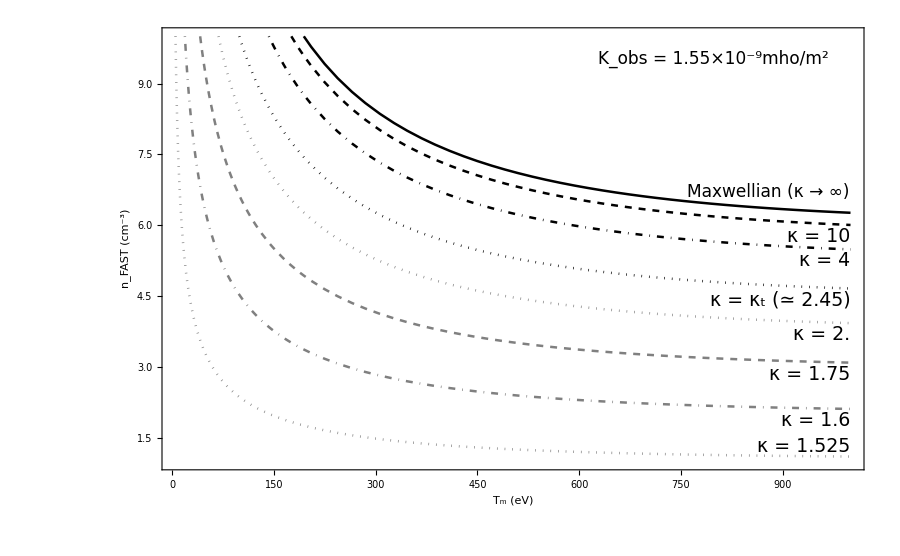

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotRange->{All,{1,10}},PlotLegends->LineLegend[Automatic],LabelStyle->(FontSize->19),Epilog->{Text[Style["K_obs = 1.55×10^-9mho/m^2",FontSize->17],Scaled[{0.95,0.95}],{1,1}],Text[Style["Maxwellian (κ → ∞)",FontSize->17],Scaled[{0.98,0.65}],{1,1}]},Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},ImageSize->900],{k,{1,2,3,4,5,6,7,8}}]]
```

```mathematica
minDens=1.70;
maxDens=2.07;
minT=127;
maxT=210;
```

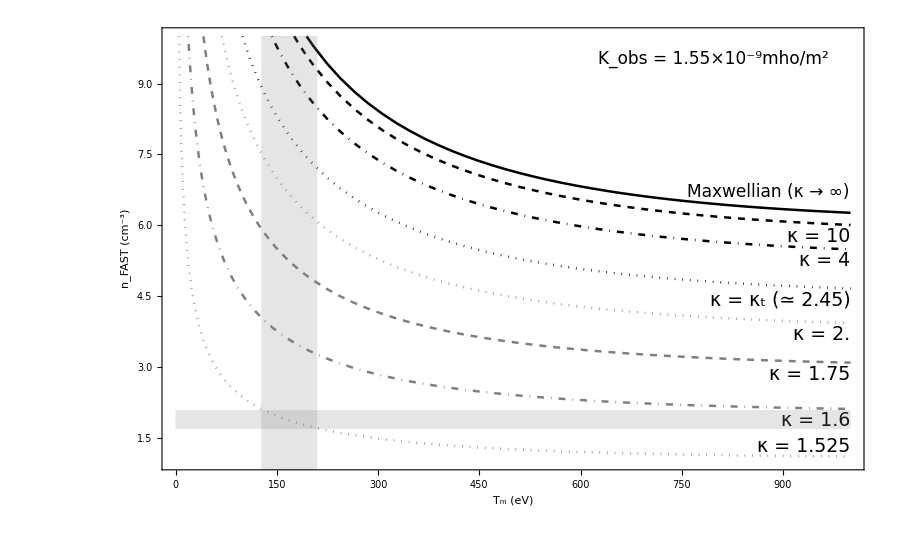

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotRange->{All,{1,10}},PlotLegends->LineLegend[Automatic],LabelStyle->(FontSize->19),Epilog->{Text[Style["K_obs = 1.55×10^-9mho/m^2",FontSize->17],Scaled[{0.95,0.95}],{1,1}],Text[Style["Maxwellian (κ → ∞)",FontSize->17],Scaled[{0.98,0.65}],{1,1}]},Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},ImageSize->900],{k,{1,2,3,4,5,6,7,8}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```